```mathematica
data={{96,72,8},{72,48,9},{288,168,10},{288,216,13},{288,240,14},{288,264,13},{216,144,12},{216,168,14},{216,192,11},{504,312,14},{504,336,11},{504,360,12},{504,384,13},{504,408,14},{504,432,14},{504,456,14},{504,480,13},{144,96,11},{384,216,14},{384,240,11},{384,264,14},{384,288,14},{384,312,14},{384,336,13},{384,360,14},{264,216,12},{264,240,11},{1056,552,12},{1056,696,13},{1056,744,14},{672,432,14},{672,456,12},{672,528,13},{672,552,12},{312,192,13},{312,240,12},{312,264,13},{312,288,12},{336,192,12},{336,216,14},{336,264,13},{336,288,14},{192,144,12},{528,288,14},{528,360,12},{528,384,13},{528,456,13},{528,504,13},{984,552,12},{984,816,13},{984,840,13},{984,912,13},{168,120,12},{240,144,13},{240,192,13},{240,216,12},{696,480,13},{696,504,12},{696,672,14},{600,360,13},{600,384,13},{600,408,14},{600,432,14},{600,456,13},{600,480,14},{600,504,14},{600,528,12},{600,552,14},{2040,1104,13},{2040,1128,14},{480,288,14},{480,312,14},{480,336,14},{480,360,13},{480,384,14},{480,432,14},{1152,672,14},{1152,744,14},{1152,864,13},{1152,984,14},{360,216,13},{360,240,14},{360,264,14},{360,288,13},{360,312,14},{360,336,14},{624,336,13},{624,384,14},{624,432,13},{624,480,14},{624,504,14},{576,336,14},{576,360,14},{576,432,13},{576,480,14},{576,528,14},{408,264,14},{408,288,13},{408,312,14},{408,336,13},{408,360,13},{408,384,13},{960,576,13},{960,624,13},{960,816,13},{960,912,14},{792,432,14},{792,480,14},{792,600,14},{792,768,13},{552,336,13},{552,360,14},{552,432,14},{552,456,14},{552,504,14},{1080,648,14},{1080,672,14},{1080,696,13},{1080,912,14},{1080,936,14},{1080,960,14},{1296,744,13},{1296,840,14},{432,240,13},{432,264,14},{432,288,13},{432,312,14},{432,336,14},{432,384,14},{768,456,14},{768,480,13},{768,504,14},{768,528,14},{768,576,14},{768,624,14},{768,720,14},{768,744,14},{1440,288,14},{1440,840,14},{1440,864,14},{1440,1032,14},{1440,1080,13},{1440,1128,14},{2208,1128,14},{2208,1224,14},{2208,1464,13},{2208,1704,14},{1536,864,14},{1536,1152,14},{864,648,14},{864,744,14},{4128,2088,14},{2016,1056,14},{2016,1512,14},{1488,1032,14},{1488,1248,14},{1488,1272,14},{720,432,14},{720,600,14},{720,696,14},{912,528,14},{912,696,14},{912,792,14},{912,816,14},{912,888,14},{1008,528,14},{1032,600,14},{1032,744,14},{1032,792,14},{1344,336,14},{1344,816,14},{3456,288,14},{1824,1128,14},{1824,1608,14},{1464,792,14},{1176,960,14},{840,672,14},{2616,1464,14},{888,624,14},{888,648,14},{888,696,14},{888,816,14},{888,864,14},{2904,2256,14},{816,576,14},{816,696,14},{1104,624,14},{1104,888,14},{1272,768,14},{1272,936,14},{2064,1128,14},{1848,984,14},{3000,1608,14},{2496,2256,14},{1944,1128,14},{2520,1320,14},{744,408,14},{744,528,14},{744,696,14},{456,360,14},{456,384,14},{1920,1152,14},{1368,792,14},{1368,840,14}};Print[ToString[Length[data]]<> " entries."]
```

204 entries.

```mathematica
connections=Map[#[[1]]->#[[2]]&,data];Print["ok"]
```

ok

```mathematica
Sort[Map[#[[2]]&,Select[Map[#[[1]]/24->#[[2]]/24&,connections],#[[1]]-1==#[[2]]&]]]
```

{2,3,8,9,10,11,12,14,15,16,20,21,28,29,31,32,36,37}

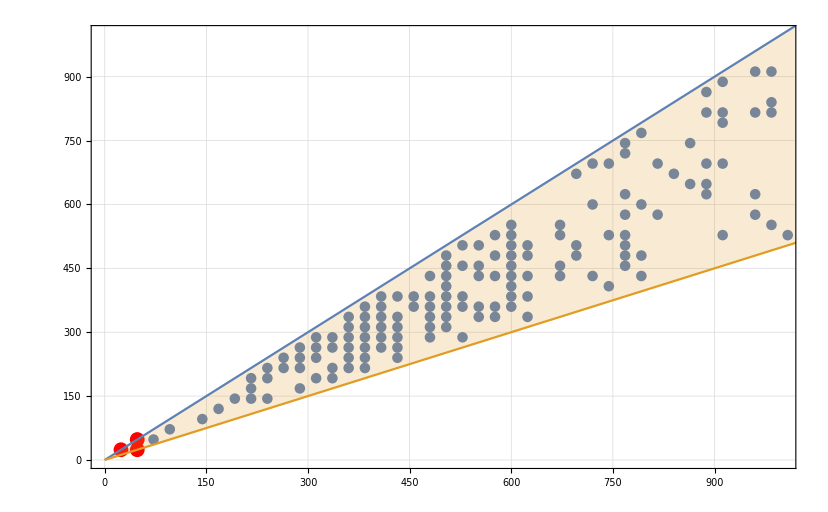

```mathematica
Show[
ListPlot[Map[{#[[1]],#[[2]]}&,connections],PlotRange->{{0,1000},{0,1000}}],
ListPlot[{{24,24},{48,24},{48,48}},PlotRange->{{0,1000},{0,1000}}, PlotStyle->Red],
Plot[{x,x/2},{x,0,5000},  Filling->{2->{1}}], Frame->True, GridLines->Automatic
]
```

```mathematica
Sort[Tally[Map[#[[3]]&,data]]]
```

{{8,2},{9,2},{10,7},{11,21},{12,56},{13,152},{14,407}}

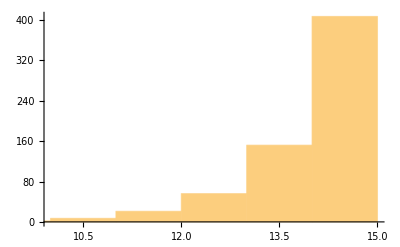

```mathematica
Histogram[Map[#[[3]]&,data]]
```

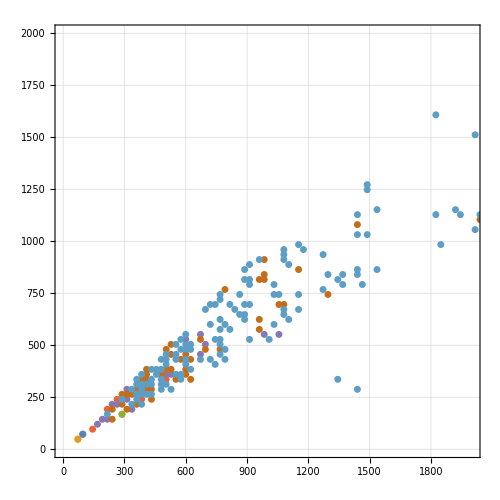

```mathematica
ListPlot[Table[Map[Tooltip[{#[[1]],#[[2]]},{ {#[[1]]->#[[2]]},#[[3]]}]&, Select[data,#[[3]]==k&]],{k,8,14}],PlotRange->{{0,2000},{0,2000}},  ImageSize->500, AspectRatio->1, PlotStyle->{PointSize[0.01]}, GridLines->Automatic,  Frame->True,ColorFunction->ColorData[3,"ColorList"]]
```

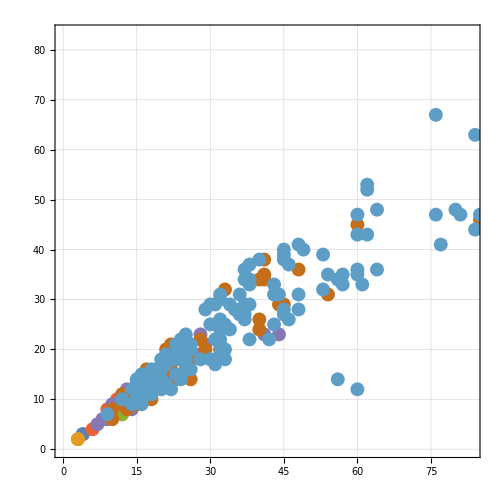

```mathematica
ListPlot[Table[Map[Tooltip[{#[[1]]/24,#[[2]]/24},{ {#[[1]]/24->#[[2]]/24},#[[3]]}]&, Select[data,#[[3]]==k&]],{k,8,14}],PlotRange->{{0,2000/24},{0,2000/24}},  ImageSize->500, AspectRatio->1, PlotStyle->{PointSize[0.02]}, GridLines->Automatic,  Frame->True,ColorFunction->ColorData[3,"ColorList"]]
```

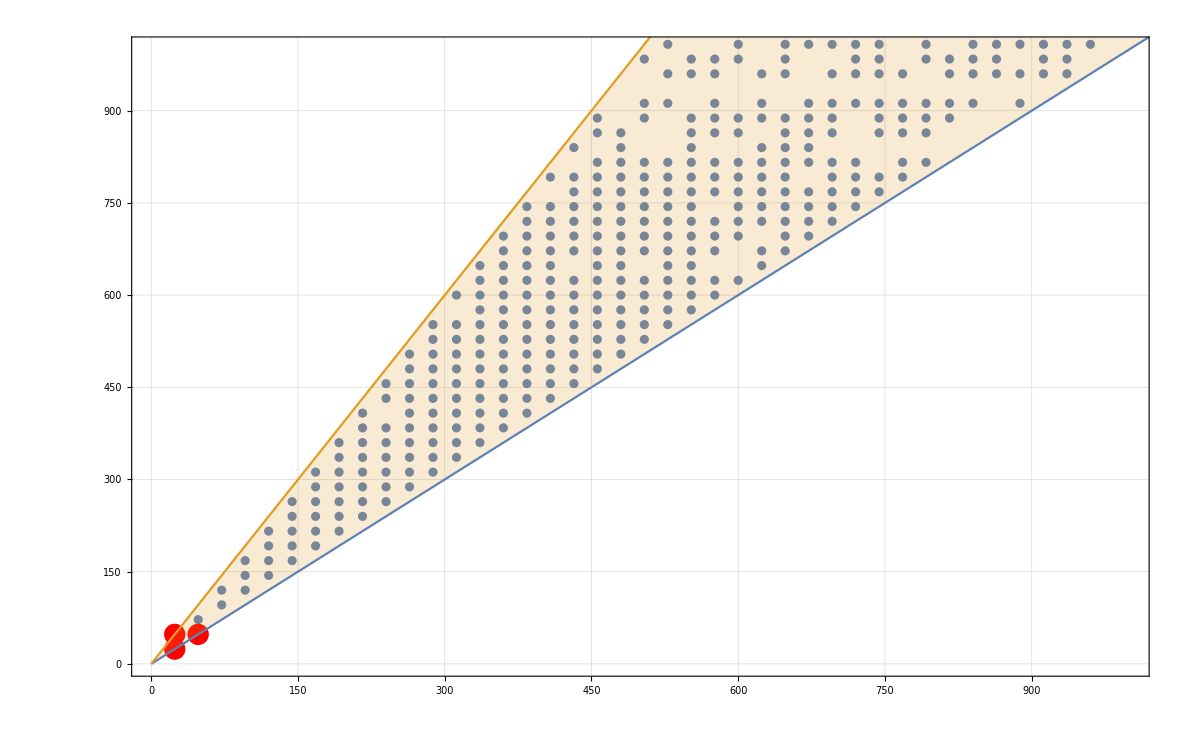

```mathematica
Show[
ListPlot[Map[{#[[2]],#[[1]]}&,connections],PlotRange->{{0,1000},{0,1000}}],
ListPlot[{{24,24},{24,48},{48,48}},PlotRange->{{0,1000},{0,1000}}, PlotStyle->Red],
Plot[{x,2x},{x,0,5000},  Filling->{2->{1}}], Frame->True, GridLines->Automatic
]
```

```mathematica
Table[Graph[Map[#[[1]]/24->#[[2]]/24&,connections], VertexLabels->"Name",GraphHighlight->Sort[Select[Map[#[[1]]/24->#[[2]]/24&,connections],#[[1]]-1==#[[2]]&]], GraphHighlightStyle->"Thick",GraphLayout->gl],{gl,{"HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}}]
```

{-Graphics-,,-Graphics-,-Graphics-,-Graphics-,}

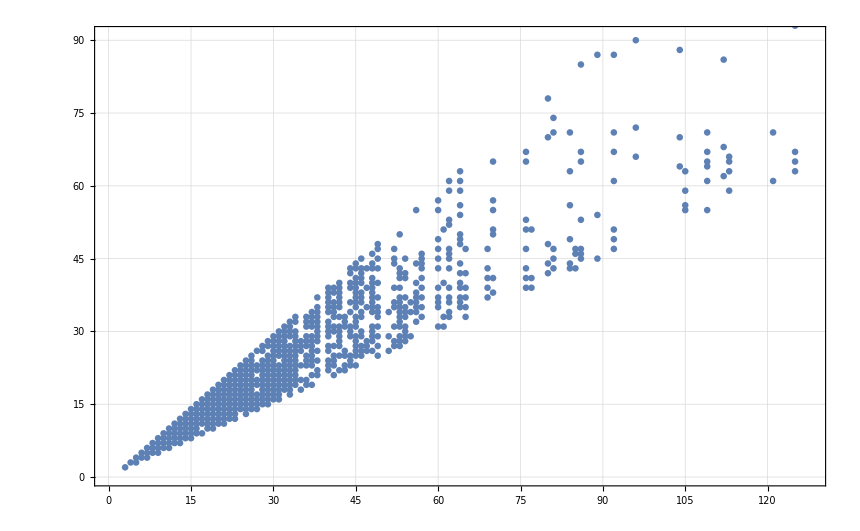

```mathematica
ListPlot[Map[Tooltip[{#[[1]]/24,#[[2]]/24}]&,connections], GridLines->Automatic, Frame->True]
```

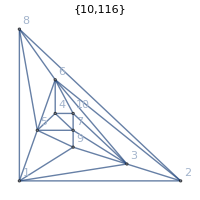
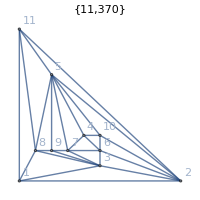
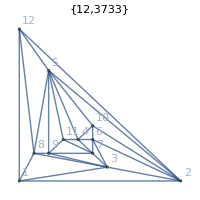
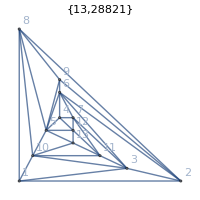
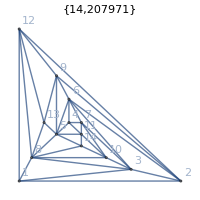

```mathematica
Row[Map[Graph[ReadGraph[#[[1]],#[[2]]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->200,PlotLabel->{#[[1]],#[[2]]}]&,{{10,116},{11,370},{12,3733},{13,28821},{14,207971}}]]
```

```mathematica
Map[ChromaticPolynomial[Graph[ReadGraph[#[[1]],#[[2]]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->200,PlotLabel->{#[[1]],#[[2]]}],4]/24&,{{10,116},{11,370},{12,3733},{13,28821},{14,207971}}]
```

{14,11,10,8,6}

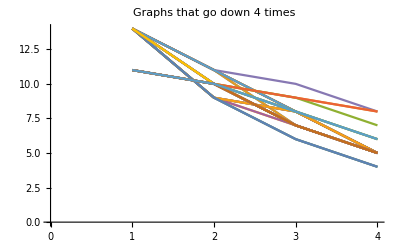

```mathematica
ListLinePlot[Flatten[Table[Table[Table[ ChromaticPolynomial[ReadGraph[ value2[[1]],value2[[2]]],4]/24,{value2, value}],{value, list}], {list,{{{{10,116},{11,370},{12,2822},{13,27451}}},{{{10,116},{11,370},{12,2822},{13,27452}}},{{{10,116},{11,370},{12,3048},{13,27451}}},{{{10,116},{11,370},{12,3048},{13,27452}}},{{{10,116},{11,370},{12,3733},{13,28821}}},{{{10,116},{11,370},{12,3750},{13,27451}}},{{{10,116},{11,370},{12,3750},{13,27452}}},{{{10,116},{11,901},{12,2822},{13,27451}}},{{{10,116},{11,901},{12,2822},{13,27452}}},{{{10,116},{11,901},{12,3048},{13,27451}}},{{{10,116},{11,901},{12,3048},{13,27452}}},{{{10,116},{11,901},{12,3750},{13,27451}}},{{{10,116},{11,901},{12,3750},{13,27452}}},{{{10,116},{11,901},{12,6692},{13,47393}}},{{{10,116},{11,901},{12,6693},{13,47393}}},{{{10,116},{11,901},{12,6695},{13,47393}}},{{{10,116},{11,917},{12,6694},{13,25685}}},{{{10,116},{11,917},{12,6694},{13,47296}}},{{{10,116},{11,917},{12,6694},{13,47396}}},{{{10,116},{11,917},{12,6748},{13,47481}}},{{{10,116},{11,946},{12,2822},{13,27451}}},{{{10,116},{11,946},{12,2822},{13,27452}}},{{{10,116},{11,946},{12,6748},{13,47481}}},{{{10,129},{11,421},{12,2822},{13,27451}}},{{{10,129},{11,421},{12,2822},{13,27452}}},{{{10,129},{11,421},{12,4064},{13,27451}}},{{{10,129},{11,421},{12,4064},{13,27452}}},{{{10,129},{11,946},{12,2822},{13,27451}}},{{{10,129},{11,946},{12,2822},{13,27452}}},{{{10,129},{11,946},{12,6748},{13,47481}}},{{{10,129},{11,421},{12,2822},{13,27451}}},{{{10,129},{11,421},{12,2822},{13,27452}}},{{{10,129},{11,421},{12,4064},{13,27451}}},{{{10,129},{11,421},{12,4064},{13,27452}}},{{{10,129},{11,946},{12,2822},{13,27451}}},{{{10,129},{11,946},{12,2822},{13,27452}}},{{{10,129},{11,946},{12,6748},{13,47481}}} }}],1], PlotLabel->"Graphs that go down 4 times"]
```

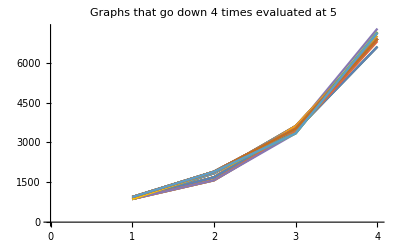

```mathematica
ListLinePlot[Flatten[Table[Table[Table[ ChromaticPolynomial[ReadGraph[ value2[[1]],value2[[2]]],5]/24,{value2, value}],{value, list}], {list,{{{{10,116},{11,370},{12,2822},{13,27451}}},{{{10,116},{11,370},{12,2822},{13,27452}}},{{{10,116},{11,370},{12,3048},{13,27451}}},{{{10,116},{11,370},{12,3048},{13,27452}}},{{{10,116},{11,370},{12,3733},{13,28821}}},{{{10,116},{11,370},{12,3750},{13,27451}}},{{{10,116},{11,370},{12,3750},{13,27452}}},{{{10,116},{11,901},{12,2822},{13,27451}}},{{{10,116},{11,901},{12,2822},{13,27452}}},{{{10,116},{11,901},{12,3048},{13,27451}}},{{{10,116},{11,901},{12,3048},{13,27452}}},{{{10,116},{11,901},{12,3750},{13,27451}}},{{{10,116},{11,901},{12,3750},{13,27452}}},{{{10,116},{11,901},{12,6692},{13,47393}}},{{{10,116},{11,901},{12,6693},{13,47393}}},{{{10,116},{11,901},{12,6695},{13,47393}}},{{{10,116},{11,917},{12,6694},{13,25685}}},{{{10,116},{11,917},{12,6694},{13,47296}}},{{{10,116},{11,917},{12,6694},{13,47396}}},{{{10,116},{11,917},{12,6748},{13,47481}}},{{{10,116},{11,946},{12,2822},{13,27451}}},{{{10,116},{11,946},{12,2822},{13,27452}}},{{{10,116},{11,946},{12,6748},{13,47481}}},{{{10,129},{11,421},{12,2822},{13,27451}}},{{{10,129},{11,421},{12,2822},{13,27452}}},{{{10,129},{11,421},{12,4064},{13,27451}}},{{{10,129},{11,421},{12,4064},{13,27452}}},{{{10,129},{11,946},{12,2822},{13,27451}}},{{{10,129},{11,946},{12,2822},{13,27452}}},{{{10,129},{11,946},{12,6748},{13,47481}}},{{{10,129},{11,421},{12,2822},{13,27451}}},{{{10,129},{11,421},{12,2822},{13,27452}}},{{{10,129},{11,421},{12,4064},{13,27451}}},{{{10,129},{11,421},{12,4064},{13,27452}}},{{{10,129},{11,946},{12,2822},{13,27451}}},{{{10,129},{11,946},{12,2822},{13,27452}}},{{{10,129},{11,946},{12,6748},{13,47481}}} }}],1], PlotLabel->"Graphs that go down 4 times evaluated at 5"]
```

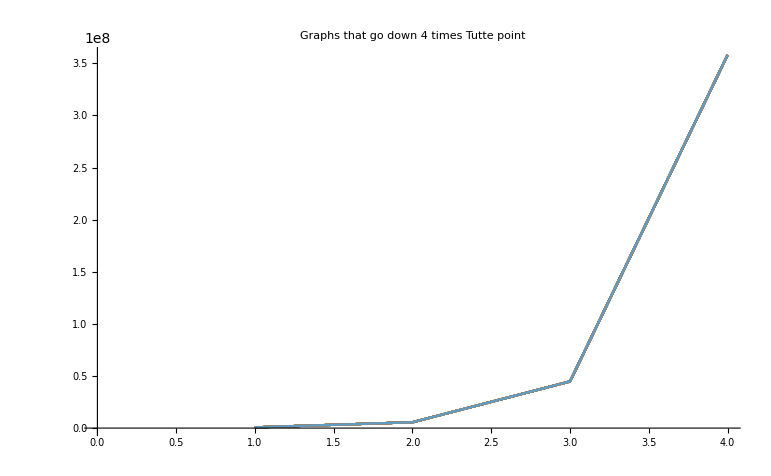

```mathematica
ListLinePlot[Flatten[Table[Table[Table[ TuttePolynomial[ReadGraph[ value2[[1]],value2[[2]]],{2,2}]/24,{value2, value}],{value, list}], {list,{{{{10,116},{11,370},{12,2822},{13,27451}}},{{{10,116},{11,370},{12,2822},{13,27452}}},{{{10,116},{11,370},{12,3048},{13,27451}}},{{{10,116},{11,370},{12,3048},{13,27452}}},{{{10,116},{11,370},{12,3733},{13,28821}}},{{{10,116},{11,370},{12,3750},{13,27451}}},{{{10,116},{11,370},{12,3750},{13,27452}}},{{{10,116},{11,901},{12,2822},{13,27451}}},{{{10,116},{11,901},{12,2822},{13,27452}}},{{{10,116},{11,901},{12,3048},{13,27451}}},{{{10,116},{11,901},{12,3048},{13,27452}}},{{{10,116},{11,901},{12,3750},{13,27451}}},{{{10,116},{11,901},{12,3750},{13,27452}}},{{{10,116},{11,901},{12,6692},{13,47393}}},{{{10,116},{11,901},{12,6693},{13,47393}}},{{{10,116},{11,901},{12,6695},{13,47393}}},{{{10,116},{11,917},{12,6694},{13,25685}}},{{{10,116},{11,917},{12,6694},{13,47296}}},{{{10,116},{11,917},{12,6694},{13,47396}}},{{{10,116},{11,917},{12,6748},{13,47481}}},{{{10,116},{11,946},{12,2822},{13,27451}}},{{{10,116},{11,946},{12,2822},{13,27452}}},{{{10,116},{11,946},{12,6748},{13,47481}}},{{{10,129},{11,421},{12,2822},{13,27451}}},{{{10,129},{11,421},{12,2822},{13,27452}}},{{{10,129},{11,421},{12,4064},{13,27451}}},{{{10,129},{11,421},{12,4064},{13,27452}}},{{{10,129},{11,946},{12,2822},{13,27451}}},{{{10,129},{11,946},{12,2822},{13,27452}}},{{{10,129},{11,946},{12,6748},{13,47481}}},{{{10,129},{11,421},{12,2822},{13,27451}}},{{{10,129},{11,421},{12,2822},{13,27452}}},{{{10,129},{11,421},{12,4064},{13,27451}}},{{{10,129},{11,421},{12,4064},{13,27452}}},{{{10,129},{11,946},{12,2822},{13,27451}}},{{{10,129},{11,946},{12,2822},{13,27452}}},{{{10,129},{11,946},{12,6748},{13,47481}}} }}],1], PlotLabel->"Graphs that go down 4 times Tutte point"]
```

```mathematica
Table[Timing[ChromaticPolynomial[ReadGraph[ n,1],4]],{n,4,20}]
```

{{0.,24},{0.,24},{0.,24},{0.,24},{0.,24},{0.015625,24},{0.,96},{0.03125,72},{0.078125,144},{0.046875,144},{0.109375,144},{0.5,768},{0.953125,912},{0.78125,912},{2.23438,696},{6.98438,3240},{8.29688,3240}}

```mathematica
Reverse[TopologicalSort[Graph[connections]]/24]
```

{35,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30,28,31,32,33,34,37,38,40,36,39,41,43,44,45,47,71,74,81,51,77,48,49,61,92,46,85,94,121,55,56,64,42,65,67,109,57,60,54,87,89,171,172,63,84,69,341,93,95,66,72,90,96,125,70,78,80,86,88,104,110,136,102,108,144,59,113,50,53,76,52,62,68,112}

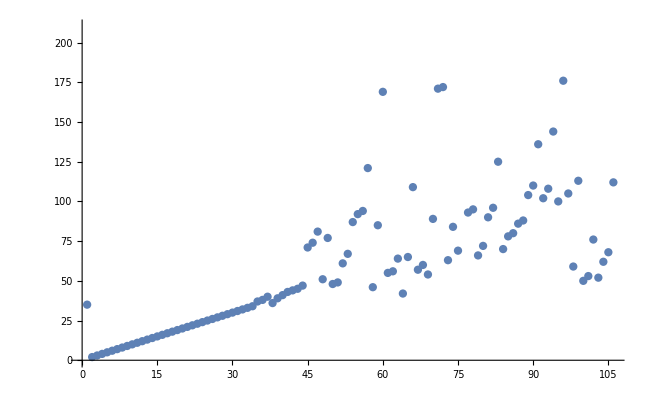

```mathematica
ListPlot[Reverse[TopologicalSort[Graph[connections]]/24]]
```

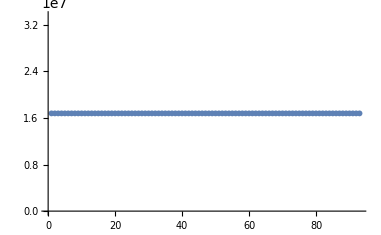

```mathematica
ListPlot[Map[TuttePolynomial[#,{2,2}]&,Select[Table[Graph[ReadGraph[10,k], GraphLayout->"PlanarEmbedding", PlotLabel->k],{k,Range[233]}],ChromaticPolynomial[#,4]==24&]]]
```

```mathematica
NSolve[TuttePolynomial[ReadGraph[10,3],{0,y}]==0]
```

{{y→-1.27399-0.356396 ⅈ},{y→-1.27399+0.356396 ⅈ},{y→-1.19579-0.688672 ⅈ},{y→-1.19579+0.688672 ⅈ},{y→-1.19191},{y→-1.01645-1.19796 ⅈ},{y→-1.01645+1.19796 ⅈ},{y→-1.},{y→-0.537183-1.4251 ⅈ},{y→-0.537183+1.4251 ⅈ},{y→0.+0. ⅈ},{y→0.016532-1.54495 ⅈ},{y→0.016532+1.54495 ⅈ},{y→0.60284-1.41228 ⅈ},{y→0.60284+1.41228 ⅈ}}

```mathematica
StreamPlot[{x*y,TuttePolynomial[ReadGraph[8,8],{x,y}]},{x,-1,1},{y,-1,1}]
```

$Aborted

```mathematica
Select[Table[Graph[ReadGraph[10,k], GraphLayout->"PlanarEmbedding", PlotLabel->k],{k,Range[233]}],ChromaticPolynomial[#,4]==24&]
```

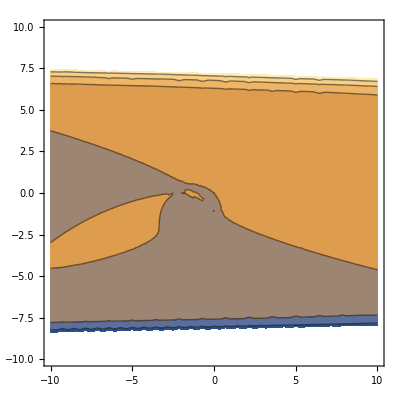
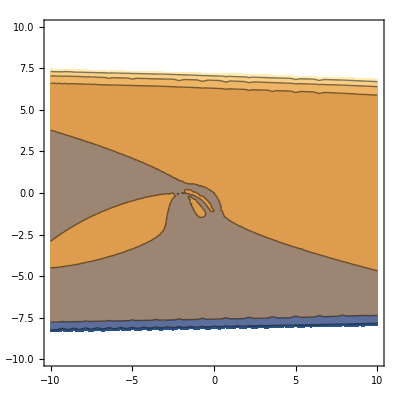
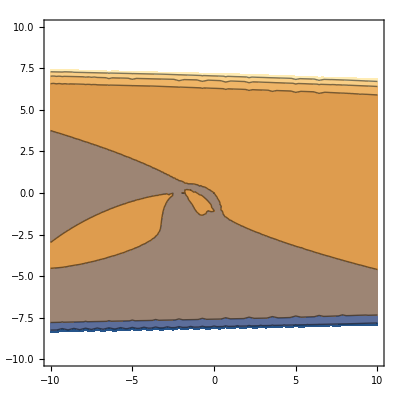
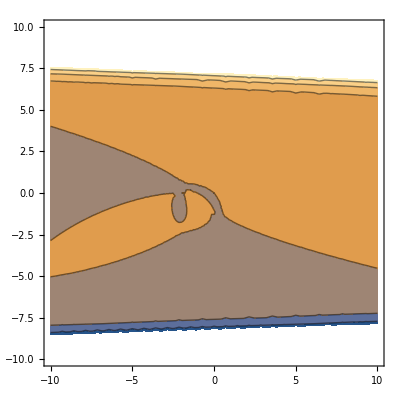
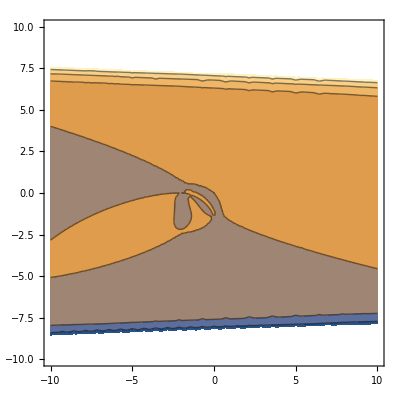
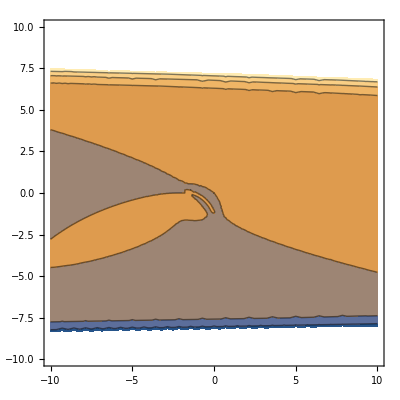
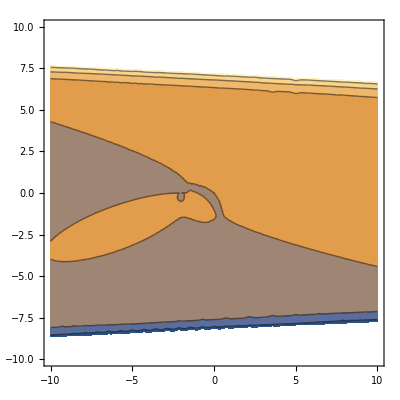

```mathematica
Map[ContourPlot[TuttePolynomial[#,{x,y}],{x,-10,10},{y,-10,10}]&,Select[Table[Graph[ReadGraph[8,k], GraphLayout->"PlanarEmbedding", PlotLabel->k],{k,Range[14]}],ChromaticPolynomial[#,4]==24&]]
```

```mathematica
Map[ContourPlot[TuttePolynomial[#,{x,y}],{x,-10,10},{y,-10,10}]&,Select[Table[Graph[ReadGraph[9,k], GraphLayout->"PlanarEmbedding", PlotLabel->k],{k,Range[50]}],ChromaticPolynomial[#,4]==24&]]
```

$Aborted

```mathematica
TuttePolynomial[ReadGraph[8,3],{2,2}]
```

262144

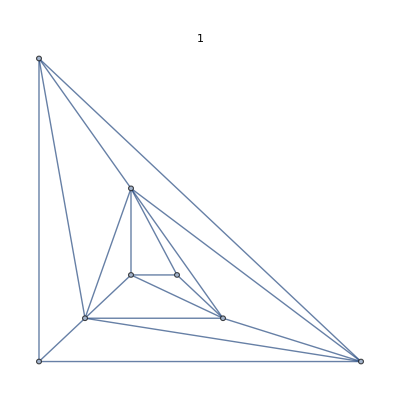
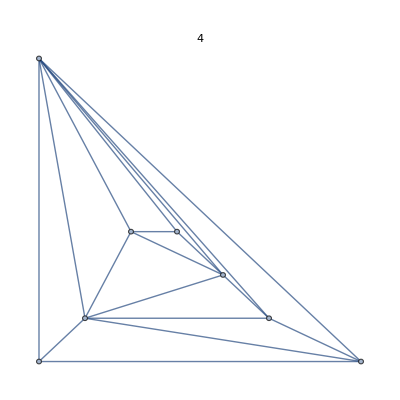
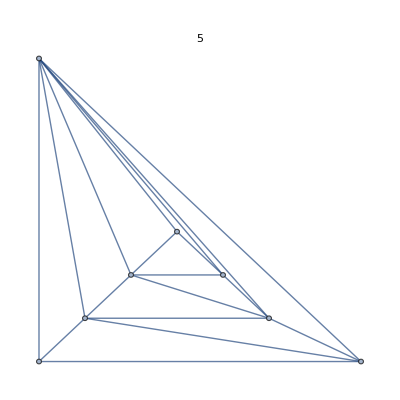
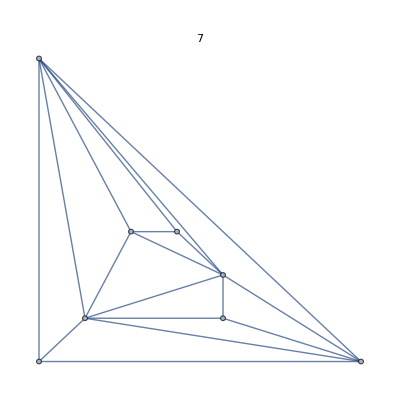
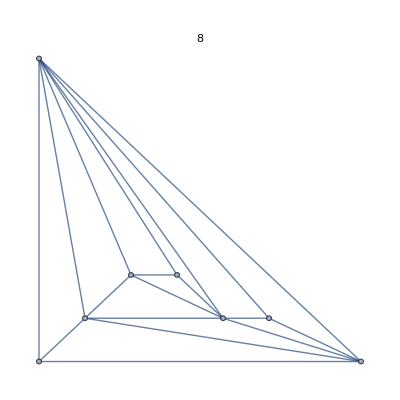
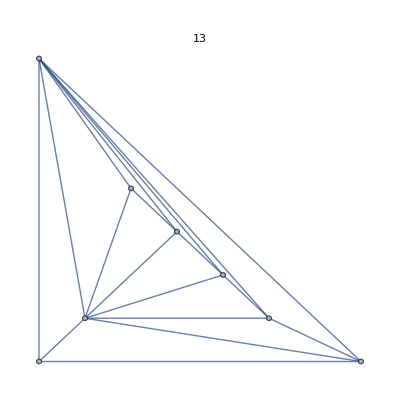
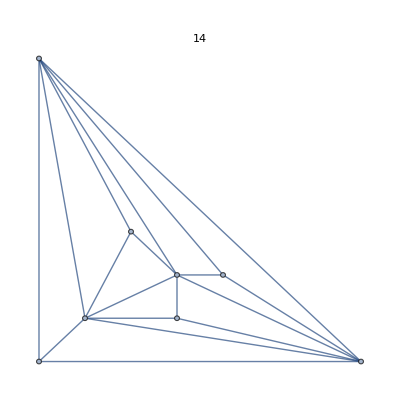

```mathematica
Select[Table[Graph[ReadGraph[8,k], GraphLayout->"PlanarEmbedding", PlotLabel->k],{k,Range[14]}],ChromaticPolynomial[#,4]==24&]
```

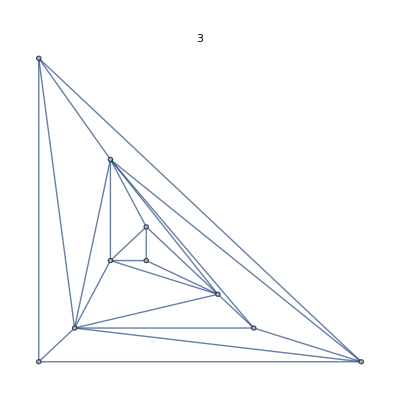
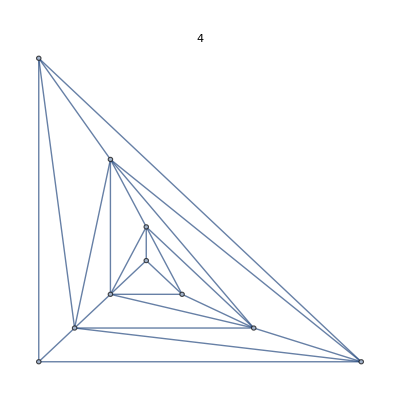
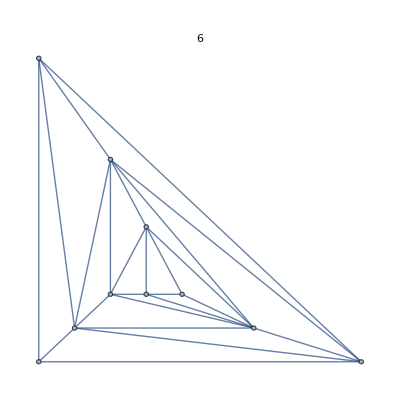
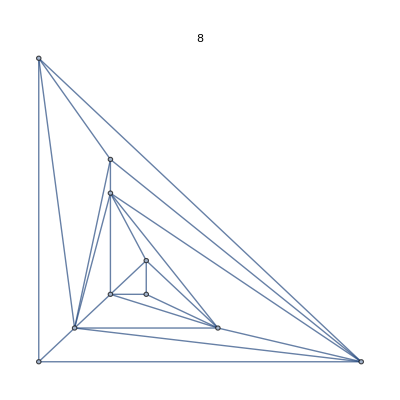
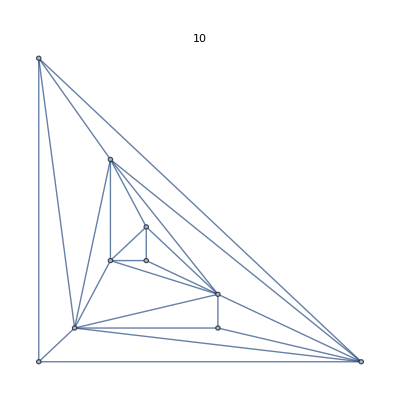
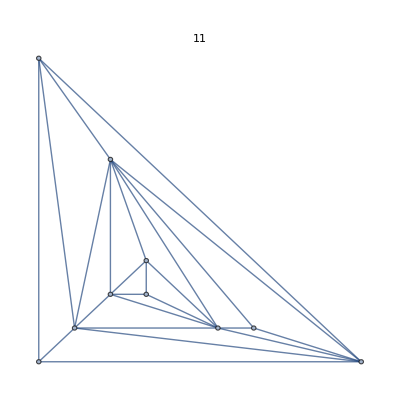
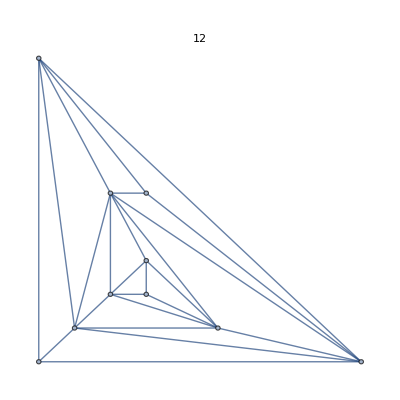
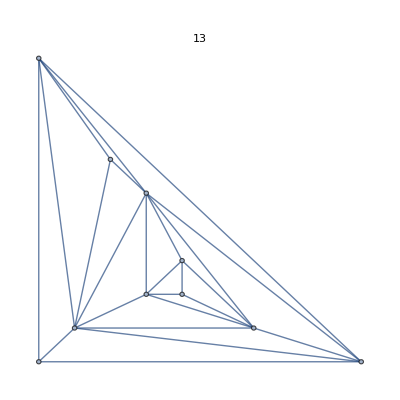

```mathematica
Select[Table[Graph[ReadGraph[10,k], GraphLayout->"PlanarEmbedding", PlotLabel->k],{k,Range[233]}],ChromaticPolynomial[#,4]==24&]
```

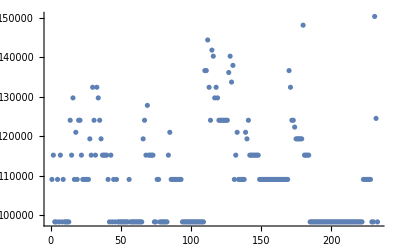

```mathematica
ListPlot[Map[TuttePolynomial[#,{2,0}]&,Table[Graph[ReadGraph[10,k], GraphLayout->"PlanarEmbedding"],{k,Range[233]}]]]
```